```mathematica
ClearAll["Global`*"]
ClearSystemCache[]
$PrePrint=MatrixForm;
```

```mathematica
(*g=0.03625; (*gamma-inverse temp*)
n=100;
nmax=4;
ncut=100;*)
```

```mathematica
f1[x_,n_,ncut_,g_]:=Sum[Exp[-g k^2 x]Product[If[j≠k,1/((1-Exp[g(k^2-j^2)])^2),1], {j,1,ncut}](x+1+2Sum[If[l≠k, 1/(1-Exp[-g(k^2-l^2)]),0], {l,ncut}]), {k,ncut}];
f2[x_,n_,ncut_,g_]:=Product[1/((1-Exp[-g j^2])^2), {j,ncut}]+Sum[Exp[-g k^2 n]/(1-Exp[g k^2])Product[If[j≠k, 1/((1-Exp[g(k^2-j^2)])^2),1],{j,ncut}](n+1+1/(1-Exp[-g k^2])+2Sum[If[l≠k,1/(1-Exp[-g(k^2-l^2)]),0],{l,1,ncut}]), {k,ncut}];
pexact[x_,n_,ncut_,g_]:=f1[x,n,ncut,g]/f2[x,n,ncut,g];

g1[x_,n_,nmax_,g_]:=g^2Sum[Exp[-g k^2x]Product[If[j≠k,1/((k^2-j^2)^2),1],{j,nmax}](x+2/g Sum[If[l≠k,1/(k^2-l^2),0],{l,nmax}]),{k,nmax}];
g2[x_,n_,nmax_,g_]:=1/(nmax!)^4-g Sum[Exp[-g k^2n]/k^2Product[If[j≠k,1/((k^2-j^2)^2),1],{j,nmax}](n+1/g(1/k^2+2Sum[If[l≠k,1/(k^2-l^2),0],{l,nmax}])), {k,nmax}];
pclass[x_,n_,nmax_,g_]:=g1[x,n,nmax,g]/g2[x,n,nmax,g];
pclassd[n_,nmax_,g_]:=Table[NIntegrate[pclass[t,n,nmax,g],{t,n x/(n+1),n(x+1)/(n+1)}],{x,0,n}];
```

General::munfl: 1.5251×10^-288 1.48487×10^-30 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.57429×10^-183 7.38164×10^-135 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.46415×10^-198 7.06579×10^-150 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.754162}. NIntegrate obtained 1.91716×10^-13 and 1.50896×10^-18 for the integral and error estimates.

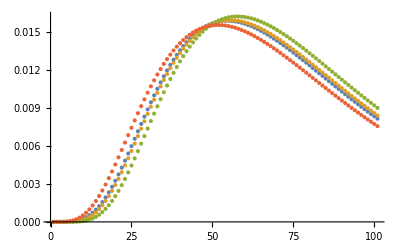

```mathematica
data=Table[pexact[x,100,70,0.03625],{x,0,100}];
datac=pclassd[100,4,0.03625];
datap=pclassd[100,4+1,0.03625];
datam=pclassd[100,4-1,0.03625];
ListPlot[{data,datac,datap,datam}]
```

```mathematica
Directory[]
Export["fit-N=100-beta=0.03625-exact.txt",data]
Export["fit-N=100-beta=0.03625-cf-ok.txt",datac]
Export["fit-N=100-beta=0.03625-cf+1.txt",datap]
Export["fit-N=100-beta=0.03625-cf-1.txt",datam]
```

```mathematica
ncut=.
dZdE[q_,n_,ncut_]:=-D[Exp[-β energy[0]n]Product[1/((1-Exp[-β(energy[j]-energy[0])])^2), {j,ncut}]+Sum[Exp[-β energy[k]n]/(1-Exp[β (energy[k]-energy[0])])Product[If[j≠k, 1/((1-Exp[β (energy[k]-energy[j])])^2),1],{j,ncut}](n+1+1/(1-Exp[-β (energy[k]-energy[0])])+2Sum[If[l≠k,1/(1-Exp[-β (energy[k]-energy[l])]),0],{l,1,ncut}]), {k,ncut}],energy[q]];
correlationExact[deltax_,n_,ncut_,g_]:=Sum[(dZdE[q,n,ncut]/.{β->1,energy[arg_]->g(arg)^2})Cos[2 Pi q deltax],{q,0,ncut}]/f2[asd,n,ncut,g]/n;
```

```mathematica
correlationExact[0,100,10,0.03625]
correlationExact[1,100,10,0.03625]
```

100.

100.

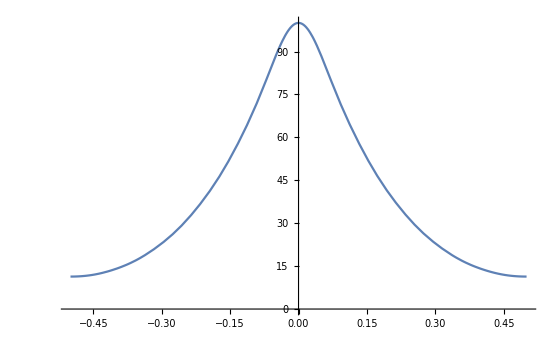

```mathematica
Plot[correlationExact[x,100,10,0.03625],{x,-0.5,0.5}]
```

```mathematica
z[x_,n_,nmax_,g_]:=1/g^(2nmax)*g2[x,n,nmax,g];
intZero[n_,nmax_,g_]:=1/g^(2nmax)*Sum[Exp[-g  p^2n] * Product[If[k≠p,1/(p^2-k^2)^2,1], {k,0,nmax}]*(n+2/g*Sum[If[l≠p,1/(p^2-l^2),0], {l,0,nmax}]), {p,0,nmax}];
int[q_,n_,nmax_,g_]:=1/g^(2nmax)*Sum[If[p≠q, Exp[-g p^2n] * 1/p^2 * 1/(p^2-q^2) * Product[If[k≠p, 1/(p^2-k^2)^2,1], {k,1,nmax}]*(n+1/g*(1/(p^2-q^2)+1/p^2+2*Sum[If[l≠p,1/(p^2-l^2),0], {l,1,nmax}])),0],{p,1,nmax}]+1/g^(2nmax+1) * 1/q^2 * Product[1/k^4, {k,1,nmax}] -1/g^(2nmax-1) * Exp[-g q^2n] * 1/q^2 * Product[If[k≠q,1/(q^2-k^2)^2,1], {k,1,nmax}]*(n^2/2+1/g*n/q^2+1/g^2 * 1/q^4+2/g*(n+1/g*1/q^2)*Sum[If[l≠q,1/(q^2-l^2),0], {l,1,nmax}]+2/g^2*Sum[If[l≠q &&l'≠q && l≠l',1/((q^2-l^2)*(q^2-l'^2)),0], {l,1,nmax},{l',1,nmax}]+3/g^2*Sum[If[l≠q,1/(q^2-l^2)^2,0], {l,1,nmax}]);
```

```mathematica
correlationClass[x_,n_,nmax_,g_]:=1/z[asd,n,nmax,g]*(intZero[n,nmax,g]+2Sum[Cos[2Pi*q*x]*int[q,n,nmax,g], {q,1,nmax}])/n;
```

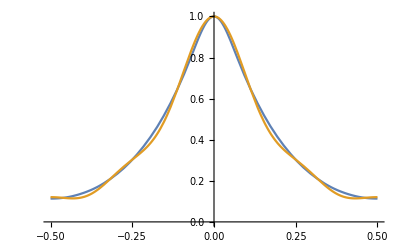

```mathematica
Plot[{correlationExact[x,100,10,0.03625],correlationClass[x,100,4,0.03625]},{x,-0.5,0.5}]
```